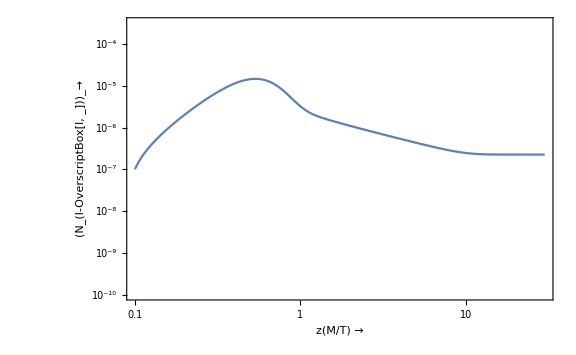

```mathematica
Parameters={Γ->10^-10  , g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn, Nl},{z, 0.1, 200}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,30}, PlotRange->{{0.1,30},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
Parameters={Γ->10^-10  , g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];


solution1= NDSolve[{Nn1'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nl1'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-1, Nl1[0.1]==10^-7}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];

solution2= NDSolve[{Nn2'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nl2'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==10^-6, Nl2[0.1]==10^-7}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[Evaluate[Nn[z]/.solution],{z, 0.1,200},PlotRange->{{0.1,300},{10^-8,10}}, Frame-> True,PlotStyle->{Blue, Dashed},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn1[z]/.solution1],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Yellow,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn2[z]/.solution2],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%]
```

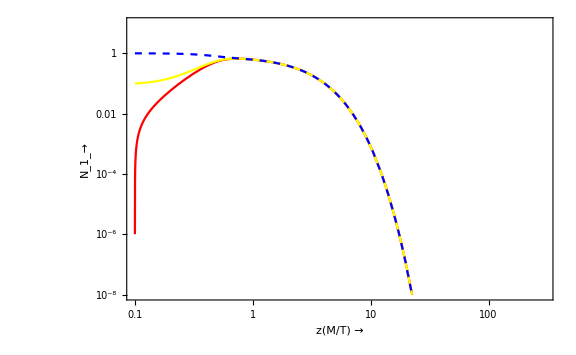

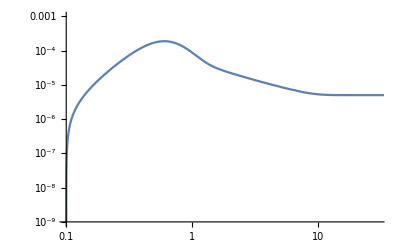

```mathematica
Parameters={Γ->10^-10  ,Γ1-> 0.5*10^-10, g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-3};
Clear[Nn,Nl, z]
solution1= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/4)*(Γ1/((4 π^3*g/45)^0.5*(M^2/Mpl)))*z^3*BesselK[1,z]*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 0.5},PrecisionGoal->3];
bc=Evaluate[Nn[0.5]/.solution1];
bc1=Evaluate[Nl[0.5]/.solution1];
solution2= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/4)*(Γ1/((4 π^3*g/45)^0.5*(M^2/Mpl)))*z^3*BesselK[1,z]*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.5]==bc, Nl[0.5]==bc1}/.Parameters,{Nn, Nl},{z, 0.5,  100},PrecisionGoal->3];

LogLogPlot[Evaluate[Nl[z]/.solution1],{z, 0.1,0.5}, PlotRange->{{0.1,30},{10^-9,10^-3}}];
LogLogPlot[Evaluate[Nl[z]/.solution2],{z, 0.5,100}, PlotRange->{{0.1,30},{10^-9,10^-3}}];
Show[%,%%]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {z,Nl[z],Nn[z]} = {0.,-0.000163623,1.00326}.

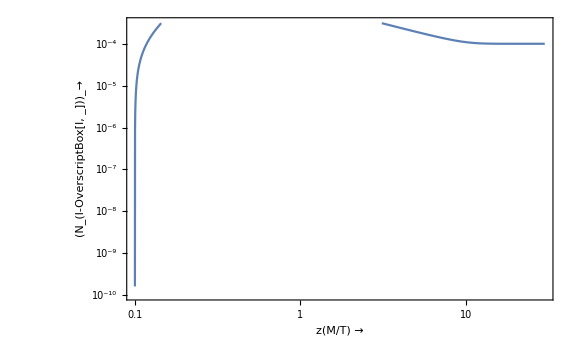

```mathematica
Parameters={Γ->10^-9  , g-> 106.75 , M->  10^3.48, Mpl-> 1.221*10^19, ϵ-> 5*10^-2};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-10}/.Parameters,{Nn[z], Nl[z]},{z, 0, 200}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z, 0.1,30}, PlotRange->{{0.1,30},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
10^-3.5 Joined->True,
```

0.000316228

```mathematica
1/10
```

1/10

OptionValue::nodef: Unknown option PlotLegends for Graphics.

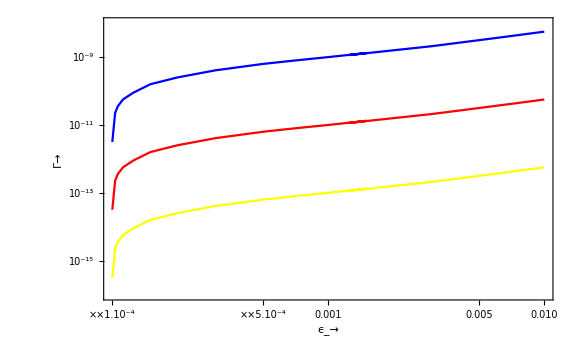

```mathematica
ListLogLogPlot[{{10^-4,10^-13.5},{1.03*10^-4,10^-12.65},{1.06*10^-4,10^-12.45},{1.12*10^-4,10^-12.25},{1.25*10^-4,10^-12.05},{1.5*10^-4,10^-11.8},{2*10^-4,10^-11.6},{3*10^-4,10^-11.39},{5*10^-4,10^-11.2},{7*10^-4,10^-11.1},{ 10^-3,10^-11} ,{ 1.5*10^-3,10^-10.88} ,{1.25* 10^-3,10^-10.94} ,{ 2*10^-3,10^-10.8} ,{ 3*10^-3,10^-10.68} ,{5 10^-3,10^-10.5} ,{ 7*10^-3,10^-10.38} ,{ 10^-2,10^-10.25} }   ,Joined->True,  PlotRange->{{10^-4,10^-2},{10^-16,10^-8}},PlotStyle->Red,Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
ListLogLogPlot[{{10^-4,10^-11.5},{1.03*10^-4,10^-10.65},{1.06*10^-4,10^-10.45},{1.12*10^-4,10^-10.25},{1.25*10^-4,10^-10.05},{1.5*10^-4,10^-9.8},{2*10^-4,10^-9.6},{3*10^-4,10^-9.39},{5*10^-4,10^-9.2},{7*10^-4,10^-9.1},{ 10^-3,10^-9} ,{ 1.5*10^-3,10^-8.88} ,{1.25* 10^-3,10^-8.94} ,{ 2*10^-3,10^-8.8} ,{ 3*10^-3,10^-8.68} ,{5 10^-3,10^-8.5} ,{ 7*10^-3,10^-8.38} ,{ 10^-2,10^-8.25} }   ,Joined->True, PlotRange->{{10^-4,10^-2},{10^-16,10^-8}},PlotLegends->"M=10^4",PlotStyle->Blue,Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
ListLogLogPlot[{{10^-4,10^-15.5},{1.03*10^-4,10^-14.65},{1.06*10^-4,10^-14.45},{1.12*10^-4,10^-14.25},{1.25*10^-4,10^-14.05},{1.5*10^-4,10^-13.8},{2*10^-4,10^-13.6},{3*10^-4,10^-13.39},{5*10^-4,10^-13.2},{7*10^-4,10^-13.1},{ 10^-3,10^-13} ,{ 1.5*10^-3,10^-12.88} ,{1.25* 10^-3,10^-12.94} ,{ 2*10^-3,10^-12.8} ,{ 3*10^-3,10^-12.68} ,{5 10^-3,10^-12.5} ,{ 7*10^-3,10^-12.38} ,{ 10^-2,10^-12.25} }   ,Joined->True, PlotRange->{{10^-4,10^-2},{10^-16,10^-8}},PlotLegends->"M=10^2", PlotStyle->Yellow,Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%,PlotLegends->"M=10^3,10^(4,)10^2"]
```

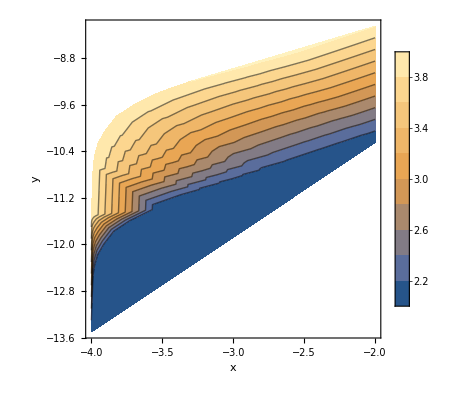

```mathematica
ListContourPlot[Log[10,Flatten[{{{10^-4,10^-13.5, 10^2},{1.03*10^-4,10^-12.65,  10^2},{1.06*10^-4,10^-12.45,  10^2},{1.12*10^-4,10^-12.25,  10^2},{1.25*10^-4,10^-12.05,  10^2},{1.5*10^-4,10^-11.8,  10^2},{2*10^-4,10^-11.6,  10^2},{3*10^-4,10^-11.39,  10^2},{5*10^-4,10^-11.2,  10^2},{7*10^-4,10^-11.1,  10^2},{ 10^-3,10^-11,  10^2} ,{ 1.5*10^-3,10^-10.88,  10^2} ,{1.25* 10^-3,10^-10.94,  10^2} ,{ 2*10^-3,10^-10.8,  10^2} ,{ 3*10^-3,10^-10.68,  10^2} ,{5 10^-3,10^-10.5,  10^2} ,{ 7*10^-3,10^-10.38,  10^2} ,{ 10^-2,0.56*10^-10,  10^2}} ,               {{10^-4,10^-11.5, 10^4},{1.03*10^-4,10^-10.65, 10^4},{1.06*10^-4,10^-10.45, 10^4},{1.12*10^-4,10^-10.25, 10^4},{1.25*10^-4,10^-10.05, 10^4},{1.5*10^-4,10^-9.8, 10^4},{2*10^-4,10^-9.6, 10^4},{3*10^-4,10^-9.39, 10^4},{5*10^-4,10^-9.2, 10^4},{7*10^-4,10^-9.1, 10^4},{ 10^-3,10^-9, 10^4} ,{ 1.5*10^-3,10^-8.88, 10^4} ,{1.25* 10^-3,10^-8.94, 10^4} ,{ 2*10^-3,10^-8.8, 10^4} ,{ 3*10^-3,10^-8.68, 10^4} ,{5 10^-3,10^-8.5, 10^4} ,{ 7*10^-3,10^-8.38, 10^4} ,{ 10^-2,0.56*10^-8, 10^4}}},1] ],AxesLabel->{"x","y","z"},PlotLegends->Automatic]
```

```mathematica
Flatten[Table[{r Cos[t],r Sin[t],5 Sinc[r]},{r,0,10,0.5},{t,-Pi,3 Pi,0.1}],1]
```

{{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},2638,{-9.33634,3.58229,-0.272011},{-9.64733,2.63232,-0.272011},{-9.86192,1.65604,-0.272011},{-9.97798,0.663219,-0.272011}}
 |  |  |  |

```mathematica
Table[{r Cos[t],r Sin[t],5 Sinc[r]},{r,0,10,0.5},{t,-Pi,3 Pi,0.1}]
```

{{{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},106,{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.},{0.,0.,5.}},19,{1}}
 |  |  |  |

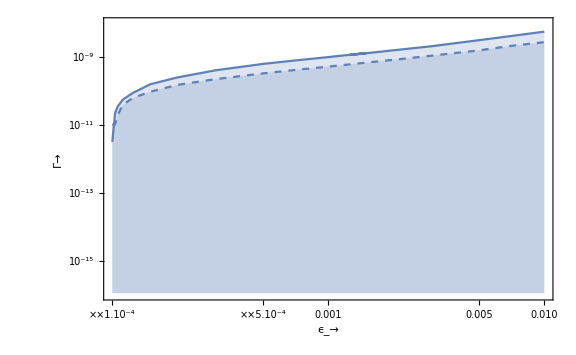

```mathematica
a1=ListLogLogPlot[{{10^-4,10^-11.5},{1.03*10^-4,10^-10.65},{1.06*10^-4,10^-10.45},{1.12*10^-4,10^-10.25},{1.25*10^-4,10^-10.05},{1.5*10^-4,10^-9.8},{2*10^-4,10^-9.6},{3*10^-4,10^-9.39},{5*10^-4,10^-9.2},{7*10^-4,10^-9.1},{ 10^-3,10^-9} ,{ 1.5*10^-3,10^-8.88} ,{1.25* 10^-3,10^-8.94} ,{ 2*10^-3,10^-8.8} ,{ 3*10^-3,10^-8.68} ,{5 10^-3,10^-8.5} ,{ 7*10^-3,10^-8.38} ,{ 10^-2,10^-8.25} }   ,Joined->True, PlotRange->{{10^-4,10^-2},{10^-16,10^-8}}, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
a2=ListLogLogPlot[{{10^-4,10^-11},{1.01*10^-4,10^-10.99},{1.03*10^-4,10^-10.98},{1.06*10^-4,10^-10.7},{1.12*10^-4,10^-10.4},{1.25*10^-4,10^-10.2},{1.5*10^-4,10^-10.02},{2*10^-4,10^-9.82},{3*10^-4,10^-9.65},{5*10^-4,10^-9.48},{7*10^-4,10^-9.38},{ 10^-3,10^-9.28} ,{ 2*10^-3,10^-9.08} ,{ 3*10^-3,10^-8.96} ,{5 10^-3,10^-8.8} ,{ 7*10^-3,10^-8.67} ,{ 10^-2,10^-8.56} }   ,PlotStyle->Dashed ,Joined->True, PlotRange->{{10^-4,10^-2},{10^-16,10^-8}}, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[a1,a2]
```

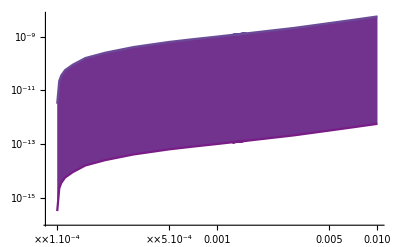

```mathematica
l1={{10^-4,10^-11.5},{1.03*10^-4,10^-10.65},{1.06*10^-4,10^-10.45},{1.12*10^-4,10^-10.25},{1.25*10^-4,10^-10.05},{1.5*10^-4,10^-9.8},{2*10^-4,10^-9.6},{3*10^-4,10^-9.39},{5*10^-4,10^-9.2},{7*10^-4,10^-9.1},{ 10^-3,10^-9} ,{ 1.5*10^-3,10^-8.88} ,{1.25* 10^-3,10^-8.94} ,{ 2*10^-3,10^-8.8} ,{ 3*10^-3,10^-8.68} ,{5 10^-3,10^-8.5} ,{ 7*10^-3,10^-8.38} ,{ 10^-2,10^-8.25} } ;
l2={{10^-4,10^-15.5},{1.03*10^-4,10^-14.65},{1.06*10^-4,10^-14.45},{1.12*10^-4,10^-14.25},{1.25*10^-4,10^-14.05},{1.5*10^-4,10^-13.8},{2*10^-4,10^-13.6},{3*10^-4,10^-13.39},{5*10^-4,10^-13.2},{7*10^-4,10^-13.1},{ 10^-3,10^-13} ,{ 1.5*10^-3,10^-12.88} ,{1.25* 10^-3,10^-12.94} ,{ 2*10^-3,10^-12.8} ,{ 3*10^-3,10^-12.68} ,{5 10^-3,10^-12.5} ,{ 7*10^-3,10^-12.38} ,{ 10^-2,10^-12.25} }   ;

Show[ListLogLogPlot[{l1,l2},Filling->{1->{2}},FillingStyle->Automatic,ColorFunction->"Rainbow", Joined->True]]
```

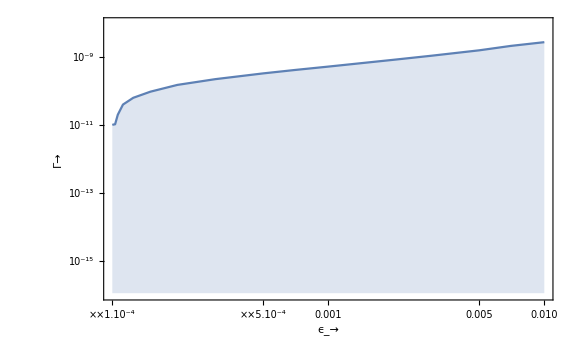

```mathematica
ListLogLogPlot[{{10^-4,10^-11},{1.01*10^-4,10^-10.99},{1.03*10^-4,10^-10.98},{1.06*10^-4,10^-10.7},{1.12*10^-4,10^-10.4},{1.25*10^-4,10^-10.2},{1.5*10^-4,10^-10.02},{2*10^-4,10^-9.82},{3*10^-4,10^-9.65},{5*10^-4,10^-9.48},{7*10^-4,10^-9.38},{ 10^-3,10^-9.28} ,{ 2*10^-3,10^-9.08} ,{ 3*10^-3,10^-8.96} ,{5 10^-3,10^-8.8} ,{ 7*10^-3,10^-8.67} ,{ 10^-2,10^-8.56} }   ,Joined->True, PlotRange->{{10^-4,10^-2},{10^-16,10^-8}}, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

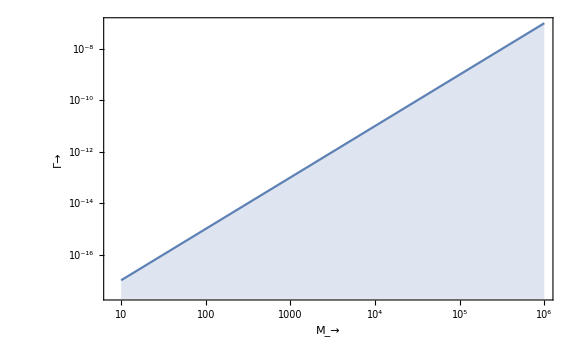

```mathematica
ListLogLogPlot[{{10,10^-17},{10^2,10^-15},{10^3,10^-13},{10^4,10^-11},{10^5,10^-9},{10^6,10^-7}},Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" M_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

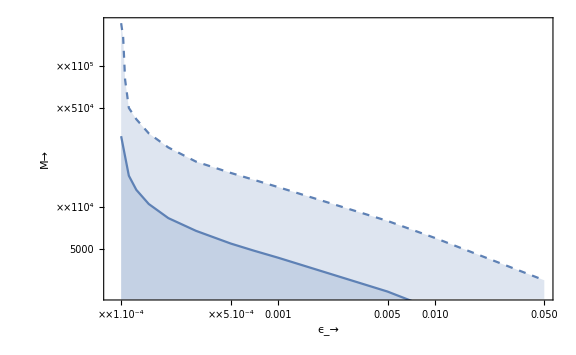

```mathematica
ListLogLogPlot[{{10^-4,10^4.5},{1.12*10^-4,10^4.22},{1.25*10^-4,10^4.12},{1.5*10^-4,10^4.02},{2*10^-4,10^3.92},{3*10^-4,10^3.83},{5*10^-4,10^3.74},{7*10^-4,10^3.69},{10^-3,10^3.64},{5*10^-3,10^3.4},{10^-2,10^3.27},{5*10^-2,10^2.98}},Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","M→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
ListLogLogPlot[{{10^-4,10^5.3},{1.03*10^-4,10^5.2},{1.06*10^-4,10^4.9},{1.12*10^-4,10^4.7},{1.25*10^-4,10^4.62},{1.5*10^-4,10^4.52},{2*10^-4,10^4.42},{3*10^-4,10^4.32},{5*10^-4,10^4.24},{10^-3,10^4.14},{5*10^-3,10^3.9},{10^-2,10^3.78},{5*10^-2,10^3.48}},PlotStyle->Dashed ,Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","M→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%]
```

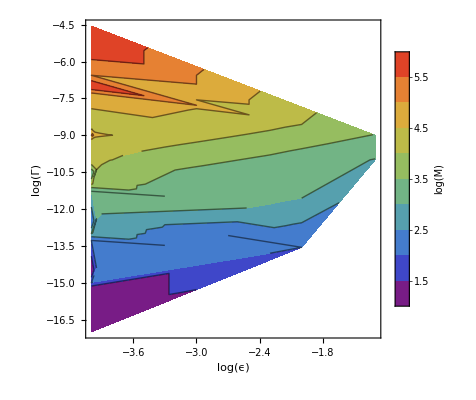

```mathematica
ListContourPlot[Log[10,Flatten[{{{10^-4,10^-11,10^4},{1.01*10^-4,10^-10.99,10^4},{1.03*10^-4,10^-10.98,10^4},{1.06*10^-4,10^-10.7,10^4},{1.12*10^-4,10^-10.4,10^4},{1.25*10^-4,10^-10.2,10^4},{1.5*10^-4,10^-10.02,10^4},{2*10^-4,10^-9.82,10^4},{3*10^-4,10^-9.65,10^4},{5*10^-4,10^-9.48,10^4},{7*10^-4,10^-9.38,10^4},{ 10^-3,10^-9.28,10^4} ,{ 2*10^-3,10^-9.08,10^4} ,{ 3*10^-3,10^-8.96,10^4} ,{5 10^-3,10^-8.8,10^4} ,{ 7*10^-3,10^-8.67,10^4} ,{ 10^-2,10^-8.56,10^4} }   ,
      {{10^-4,10^-13,10^3},{1.01*10^-4,10^-12.99,10^3},{1.03*10^-4,10^-12.98,10^3},{1.06*10^-4,10^-12.7,10^3},{1.12*10^-4,10^-12.4,10^3},{1.25*10^-4,10^-12.2,10^3},{1.5*10^-4,10^-12.02,10^3},{2*10^-4,10^-11.82,10^3},{3*10^-4,10^-11.65,10^3},{5*10^-4,10^-11.48,10^3},{7*10^-4,10^-11.38,10^3},{ 10^-3,10^-11.28,10^3} ,{ 2*10^-3,10^-11.08,10^3} ,{ 3*10^-3,10^-11.96,10^3} ,{5 10^-3,10^-11.8,10^3} ,{ 7*10^-3,10^-11.67,10^3} ,{ 10^-2,10^-11.56,10^3} }   ,     
{{10^-4,10^-15,10^2},{1.01*10^-4,10^-14.99,10^2},{1.03*10^-4,10^-14.98,10^2},{1.06*10^-4,10^-14.7,10^2},{1.12*10^-4,10^-14.4,10^2},{1.25*10^-4,10^-14.2,10^2},{1.5*10^-4,10^-14.02,10^2},{2*10^-4,10^-13.82,10^2},{3*10^-4,10^-13.65,10^2},{5*10^-4,10^-13.48,10^2},{7*10^-4,10^-13.38,10^2},{ 10^-3,10^-13.28,10^2} ,{ 2*10^-3,10^-13.08,10^2} ,{ 3*10^-3,10^-13.96,10^2} ,{5 10^-3,10^-13.8,10^2} ,{ 7*10^-3,10^-13.67,10^2} ,{ 10^-2,10^-13.56,10^2} }   ,    

{{10^-4,10^-17,10},{10^-4,10^-15,10^2},{10^-4,10^-13,10^3},{10^-4,10^-11,10^4},{10^-4,10^-9,10^5},{10^-4,10^-7,10^6}},
{{10^-4,10^-15.28,10},{10^-4,10^-13.28,10^2},{10^-4,10^-11.28,10^3},{10^-4,10^-9.28,10^4},{10^-4,10^-7.28,10^5},{10^-4,10^-5.28,10^6}},
{{10^-4,10^-14.56,10},{10^-4,10^-12.56,10^2},{10^-4,10^-10.56,10^3},{10^-4,10^-8.56,10^4},{10^-4,10^-6.56,10^5},{10^-4,10^-4.56,10^6}},

{{10^-4,10^-10,10^4.5},{1.12*10^-4,10^-10,10^4.22},{1.25*10^-4,10^-10,10^4.12},{1.5*10^-4,10^-10,10^4.02},{2*10^-4,10^-10,10^3.92},{3*10^-4,10^-10,10^3.83},{5*10^-4,10^-10,10^3.74},{7*10^-4,10^-10,10^3.69},{10^-3,10^-10,10^3.64},{5*10^-3,10^-10,10^3.4},{10^-2,10^-10,10^3.27},{5*10^-2,10^-10,10^2.98}}, 
{{10^-4,10^-9,10^5.3},{1.03*10^-4,10^-9,10^5.2},{1.06*10^-4,10^-9,10^4.9},{1.12*10^-4,10^-9,10^4.7},{1.25*10^-4,10^-9,10^4.62},{1.5*10^-4,10^-9,10^4.52},{2*10^-4,10^-9,10^4.42},{3*10^-4,10^-9,10^4.32},{5*10^-4,10^-9,10^4.24},{10^-3,10^-9,10^4.14},{5*10^-3,10^-9,10^3.9},{10^-2,10^-9,10^3.78},{5*10^-2,10^-9,10^3.48}}},1] ], ColorFunction->"Rainbow",PlotRange-> Automatic, PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"log(M)"],Right]}, FrameLabel->{"log(ϵ)","log(Γ)"},Frame-> True,FrameTicksStyle->Directive[Black,12],LabelStyle->Directive[Black,Bold, Medium]]
```

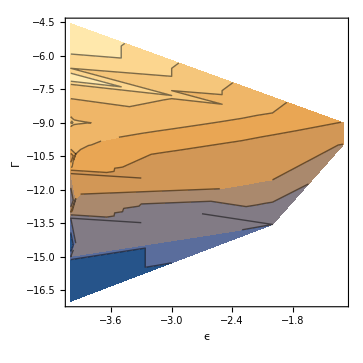
```mathematica
-Graphics--Graphics3D-
```

```mathematica
ListPlot3D[Log[10,Flatten[{{{10^-4,10^-11,10^4},{1.01*10^-4,10^-10.99,10^4},{1.03*10^-4,10^-10.98,10^4},{1.06*10^-4,10^-10.7,10^4},{1.12*10^-4,10^-10.4,10^4},{1.25*10^-4,10^-10.2,10^4},{1.5*10^-4,10^-10.02,10^4},{2*10^-4,10^-9.82,10^4},{3*10^-4,10^-9.65,10^4},{5*10^-4,10^-9.48,10^4},{7*10^-4,10^-9.38,10^4},{ 10^-3,10^-9.28,10^4} ,{ 2*10^-3,10^-9.08,10^4} ,{ 3*10^-3,10^-8.96,10^4} ,{5 10^-3,10^-8.8,10^4} ,{ 7*10^-3,10^-8.67,10^4} ,{ 10^-2,10^-8.56,10^4} }   ,
      {{10^-4,10^-13,10^3},{1.01*10^-4,10^-12.99,10^3},{1.03*10^-4,10^-12.98,10^3},{1.06*10^-4,10^-12.7,10^3},{1.12*10^-4,10^-12.4,10^3},{1.25*10^-4,10^-12.2,10^3},{1.5*10^-4,10^-12.02,10^3},{2*10^-4,10^-11.82,10^3},{3*10^-4,10^-11.65,10^3},{5*10^-4,10^-11.48,10^3},{7*10^-4,10^-11.38,10^3},{ 10^-3,10^-11.28,10^3} ,{ 2*10^-3,10^-11.08,10^3} ,{ 3*10^-3,10^-11.96,10^3} ,{5 10^-3,10^-11.8,10^3} ,{ 7*10^-3,10^-11.67,10^3} ,{ 10^-2,10^-11.56,10^3} }   ,     
{{10^-4,10^-15,10^2},{1.01*10^-4,10^-14.99,10^2},{1.03*10^-4,10^-14.98,10^2},{1.06*10^-4,10^-14.7,10^2},{1.12*10^-4,10^-14.4,10^2},{1.25*10^-4,10^-14.2,10^2},{1.5*10^-4,10^-14.02,10^2},{2*10^-4,10^-13.82,10^2},{3*10^-4,10^-13.65,10^2},{5*10^-4,10^-13.48,10^2},{7*10^-4,10^-13.38,10^2},{ 10^-3,10^-13.28,10^2} ,{ 2*10^-3,10^-13.08,10^2} ,{ 3*10^-3,10^-13.96,10^2} ,{5 10^-3,10^-13.8,10^2} ,{ 7*10^-3,10^-13.67,10^2} ,{ 10^-2,10^-13.56,10^2} }   ,    

{{10^-4,10^-17,10},{10^-4,10^-15,10^2},{10^-4,10^-13,10^3},{10^-4,10^-11,10^4},{10^-4,10^-9,10^5},{10^-4,10^-7,10^6}},
{{10^-4,10^-15.28,10},{10^-4,10^-13.28,10^2},{10^-4,10^-11.28,10^3},{10^-4,10^-9.28,10^4},{10^-4,10^-7.28,10^5},{10^-4,10^-5.28,10^6}},
{{10^-4,10^-14.56,10},{10^-4,10^-12.56,10^2},{10^-4,10^-10.56,10^3},{10^-4,10^-8.56,10^4},{10^-4,10^-6.56,10^5},{10^-4,10^-4.56,10^6}},

{{10^-4,10^-10,10^4.5},{1.12*10^-4,10^-10,10^4.22},{1.25*10^-4,10^-10,10^4.12},{1.5*10^-4,10^-10,10^4.02},{2*10^-4,10^-10,10^3.92},{3*10^-4,10^-10,10^3.83},{5*10^-4,10^-10,10^3.74},{7*10^-4,10^-10,10^3.69},{10^-3,10^-10,10^3.64},{5*10^-3,10^-10,10^3.4},{10^-2,10^-10,10^3.27},{5*10^-2,10^-10,10^2.98}}, 
{{10^-4,10^-9,10^5.3},{1.03*10^-4,10^-9,10^5.2},{1.06*10^-4,10^-9,10^4.9},{1.12*10^-4,10^-9,10^4.7},{1.25*10^-4,10^-9,10^4.62},{1.5*10^-4,10^-9,10^4.52},{2*10^-4,10^-9,10^4.42},{3*10^-4,10^-9,10^4.32},{5*10^-4,10^-9,10^4.24},{10^-3,10^-9,10^4.14},{5*10^-3,10^-9,10^3.9},{10^-2,10^-9,10^3.78},{5*10^-2,10^-9,10^3.48}}},1] ], PlotRange-> Automatic, AxesLabel->{"ϵ","Γ","M"}]
```

-Graphics3D-

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {z,Nl[z],Nn[z]} = {0.,-3.15297×10^-11,1.}.

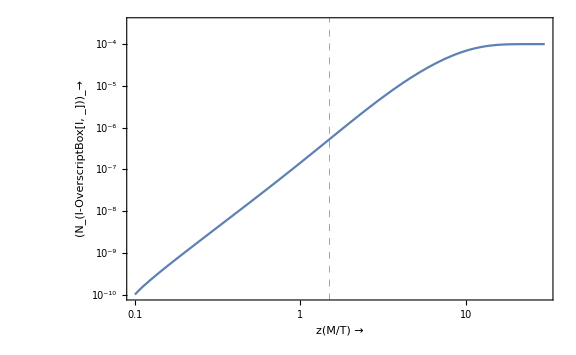

```mathematica
Parameters={Γ->10^-15  , g-> 106.75 , M->  150, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-10}/.Parameters,{Nn[z], Nl[z]},{z, 0, 200}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z, 0.1,30}, GridLines->{{1.5},{}},GridLinesStyle->Directive[Gray, Dashed] ,PlotRange->{{0.1,30},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

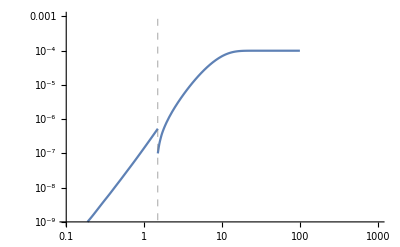

```mathematica
Parameters={Γ->10^-15  ,Γ1-> 0.5*10^-15, g-> 106.75 , M->  150, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn,Nl, z]
solution1= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/4)*(Γ1/((4 π^3*g/45)^0.5*(M^2/Mpl)))*z^3*BesselK[1,z]*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 1.5},PrecisionGoal->3];
bc=Evaluate[Nn[1.5]/.solution1];
bc1=10^-7;
solution2= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/4)*(Γ1/((4 π^3*g/45)^0.5*(M^2/Mpl)))*z^3*BesselK[1,z]*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[1.5]==bc, Nl[1.5]==bc1}/.Parameters,{Nn[z], Nl[z]},{z, 1.5,  100},PrecisionGoal->3];

LogLogPlot[Evaluate[Nl[z]/.solution1],{z, 0.1,1.5}, GridLines->{{1.5},{}},GridLinesStyle->Directive[Gray, Dashed] , PlotRange->{{0.1,100},{10^-9,10^-3}}];
LogLogPlot[Evaluate[Nl[z]/.solution2],{z, 1.5,100}, GridLines->{{1.5},{}},GridLinesStyle->Directive[Gray, Dashed] , PlotRange->{{0.1,1000},{10^-9,10^-3}}];
Show[%,%%]
```

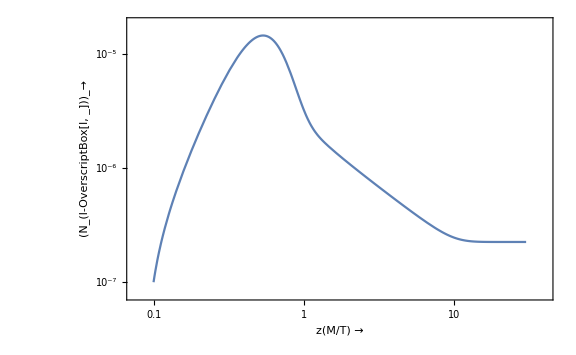

```mathematica
Parameters={Γ->10^-10  , g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,30}, PlotRange->Automatic,Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

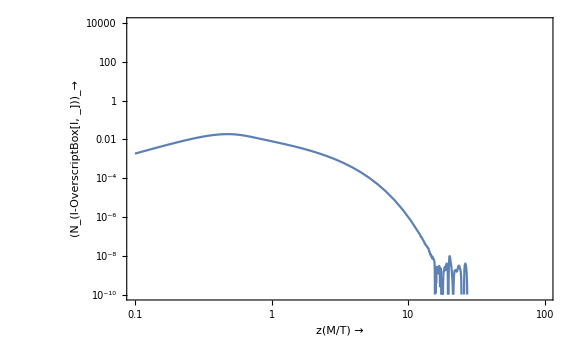

```mathematica
Parameters={Γ->10^-9  , g-> 106.75 , M->  3000, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ*0.5/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==3/4, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 100}];

LogLogPlot[Evaluate[(Nn[z]-(3/8)*z^2*BesselK[2,z])/.solution],{z,0.1,100}, PlotRange->{{0.1,100},{10^-10,10^4}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
Parameters={Γ->10^-12  , g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
 M=  1000;
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==10^-7}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

 M= 100;
solution1= NDSolve[{Nn1'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nl1'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==10^-3, Nl1[0.1]==10^-7}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];
 M=10000;
solution2= NDSolve[{Nn2'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nl2'[z]== -(1/2)*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl2[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn2[z]-(3/8)*z^2*BesselK[2,z]), Nn2[0.1]==10^-6, Nl2[0.1]==10^-7}/.Parameters,{Nn2[z], Nl2[z]},{z, 0.1, 200}];


LogLogPlot[Evaluate[Nn[z]/.solution],{z, 0.1,200},PlotRange->{{0.1,300},{10^-8,10}}, Frame-> True,PlotStyle->{Blue, Dashed},FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn1[z]/.solution1],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Yellow,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[Nn2[z]/.solution2],{z, 0.1,100}, PlotRange->{{0.1,300},{10^-8,10}},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_1_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];

Show[%,%%,%%%]
```

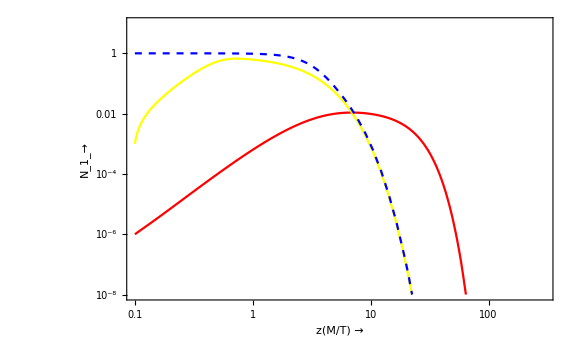

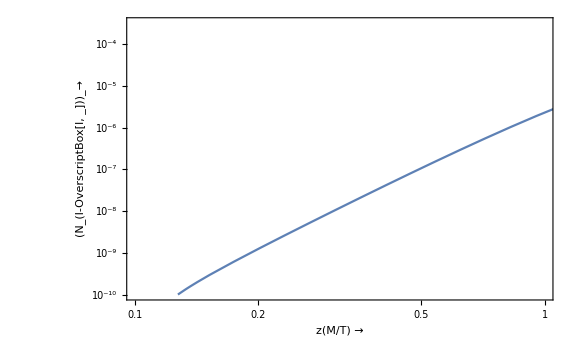

```mathematica
Parameters={Γ->10^-10.55 , g-> 106.75 , M-> 1000, Mpl-> 1.221*10^19, ϵ-> 1*10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ*0.5/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==3/4, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 100}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,100},  PlotRange->{{0.1,1},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
ListLogLogPlot[{{10^2,10^-15},{10^3,10^-13},{10^4,10^-11},{10^5,10^-9}},Joined->True, PlotRange->All,  Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" M_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
ListLogLogPlot[{{10^2,10^-12.55},{10^3,10^-10.55},{10^4,10^-8.56},{10^5,10^-6.55}},Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" M_→","Γ→"},PlotStyle->Red ,LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%]
```

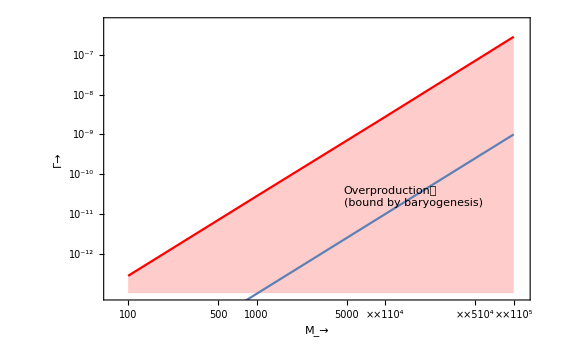

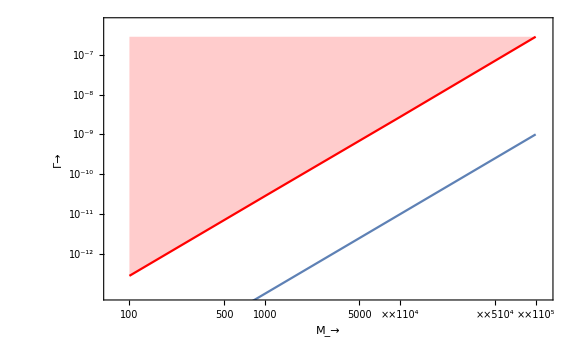

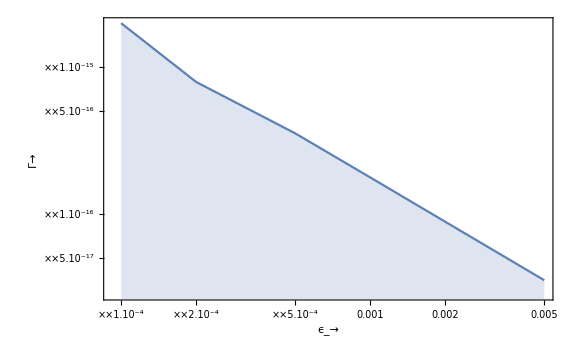

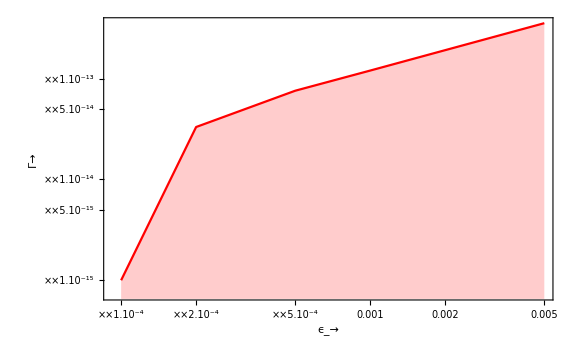

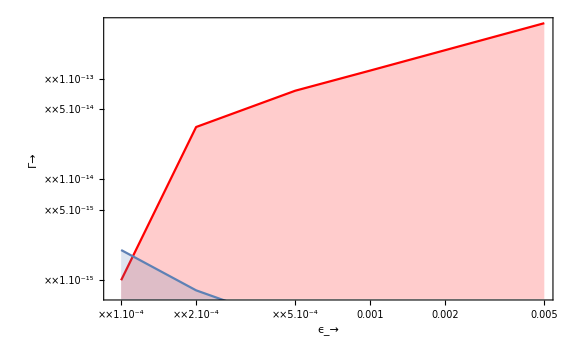

```mathematica
ListLogLogPlot[{{10^-4,10^-14.7},{2*10^-4,10^-15.1},{5*10^-4,10^-15.45},{ 10^-3,10^-15.75} ,{5 10^-3,10^-16.45} }   ,Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
ListLogLogPlot[{{10^-4,10^-15},{2*10^-4,10^-13.48},{5*10^-4,10^-13.12},{ 10^-3,10^-12.92} ,{5 10^-3,10^-12.45} }   ,PlotStyle->Red ,Joined->True, PlotRange->All, Filling->Axis, Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{" ϵ_→","Γ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]

Show[%,%%]
```

{0.000288941}

{9.0851×10^-9}

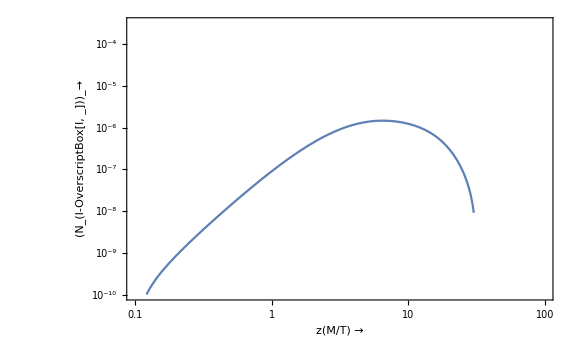

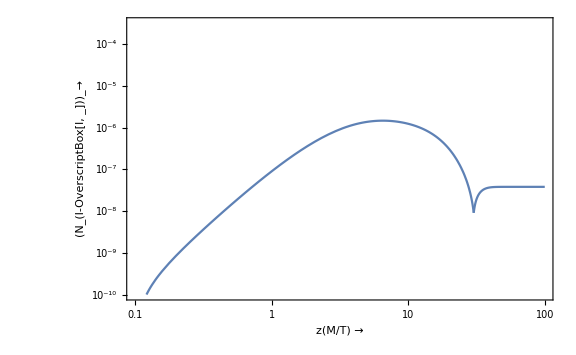

```mathematica
Parameters={Γ->10^-10  ,k->0.01,  g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-4, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 100}];
bc=Evaluate[Nn[30.2]/.solution]
bc1=Evaluate[Nl[30.2]/.solution]
solution1= NDSolve[{
Nn'[z]== -z * k * (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[30.2]==bc, Nl[30.2]==bc1}/.Parameters,{Nn, Nl},{z,30.2,  100},PrecisionGoal->3];
LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,30.2}, PlotRange->{{0.1,100},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
LogLogPlot[Evaluate[Nl[z]/.solution1],{z,30.2,100}, PlotRange->{{0.1,100},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%]
```

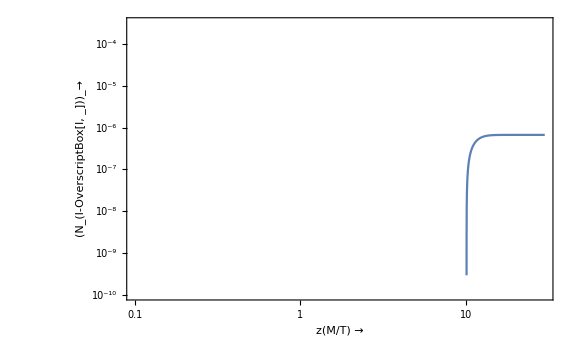

```mathematica
Parameters={Γ->10^-10  ,k->0.1,  g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==10^-4, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 200}];

LogLogPlot[Evaluate[Nl[z]/.solution],{z,0.1,30}, PlotRange->{{0.1,30},{10^-10,10^-3.5}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","(N_(l-OverscriptBox[l, _]))_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

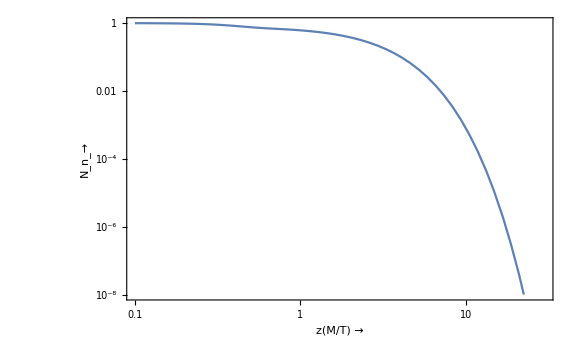

```mathematica
Parameters={k->100,  g-> 106.75 , M->  10^3, Mpl-> 1.221*10^19, ϵ-> 10^-4};
Clear[Nn, Nl, z]
solution= NDSolve[{
Nn'[z]== -z * k* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), 
Nl'[z]== -(1/2)*(z * k* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] -ϵ*(z * k)* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==1, Nl[0.1]==0}/.Parameters,{Nn, Nl},{z, 0.1, 30}];

LogLogPlot[Evaluate[Nn[z]/.solution],{z,0.1,30}, PlotRange->{{0.1,30},{10^-8,1}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"z(M/T) →","N_n_→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
Parameters={Γ->10 , g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
Clear[Nn, Nl,Nn1,Nl1,Nn2, Nl2,z]
 M=  10^10;
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ*0.5*(1-ϵ)/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==3/4, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 200}];

 M= 10^10;
solution1= NDSolve[{Nn1'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn1[z]-(3/8)*z^2*BesselK[2,z]), Nl1'[z]== -(1/2)*(z * (Γ*0.5*(1-ϵ)/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl1[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn1[1z]-(3/8)*z^2*BesselK[2,z]), Nn1[0.1]==0, Nl1[0.1]==0}/.Parameters,{Nn1[z], Nl1[z]},{z, 0.1, 200}];

LogLogPlot[Evaluate[Abs[Nn[z]]/.solution],{z, 0.1,200},PlotRange->{{0.1,200},{10^-4,1}}, Frame-> True,PlotStyle->Green,PlotLegends->{"N_N_R^in=3/4"},FrameTicksStyle->Directive[Black,18],FrameLabel->{"z(M/T) →","N_N_R_→"},LabelStyle->Directive[Black,Bold, Medium,18],ImageSize->Large];
LogLogPlot[Evaluate[Abs[Nn1[z]]/.solution1],{z, 0.1,200}, PlotRange->{{0.1,200},{10^-4,1}},PlotLegends->{"N_N_R^in=0"},Frame-> True,PlotStyle->Red,  FrameTicksStyle->Directive[Black,18],FrameLabel->{"z(M/T) →","N_N_R_→"},LabelStyle->Directive[Black,Bold, Medium,18],ImageSize->Large];
LogLogPlot[(3/8)*z^2*BesselK[2,z],{z, 0.1,200}, PlotRange->{{0.1,200},{10^-4,1}},PlotLegends->{"N_N_R^eq"},Frame-> True,PlotStyle->{Blue, Dashed},  FrameTicksStyle->Directive[Black,18],FrameLabel->{"z(M/T) →","N_N_R_→"},LabelStyle->Directive[Black,Bold, Medium,18],ImageSize->Large];

Show[%,%%,%%%]
```

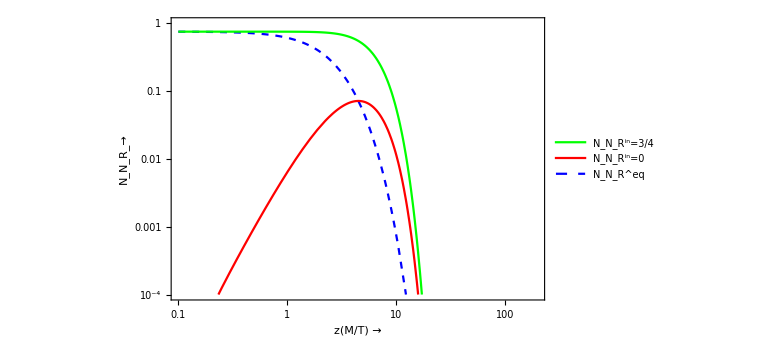

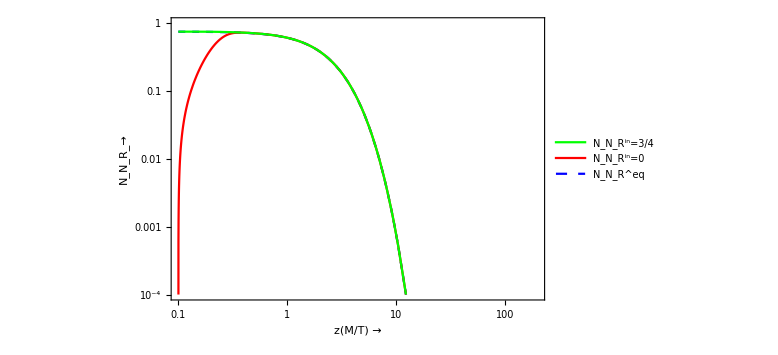

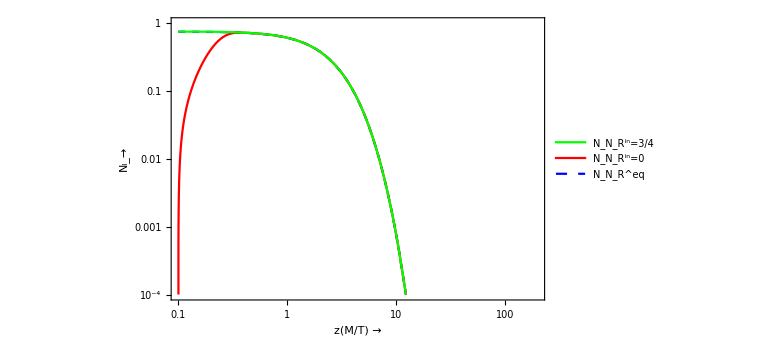

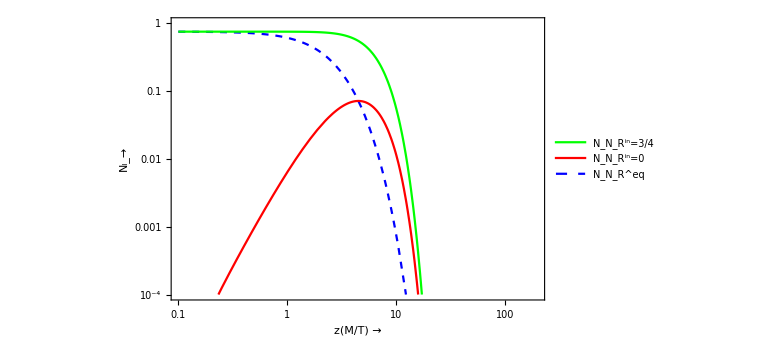

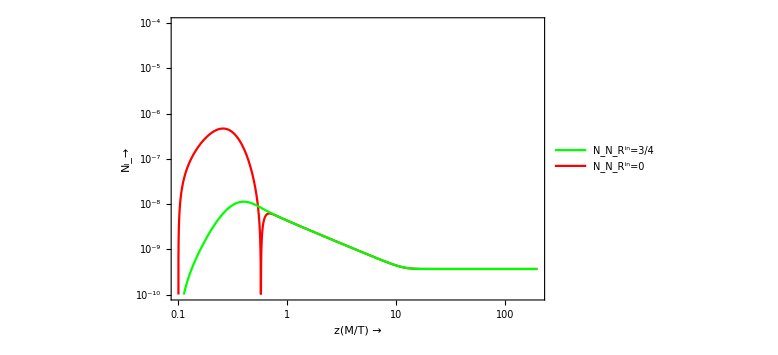

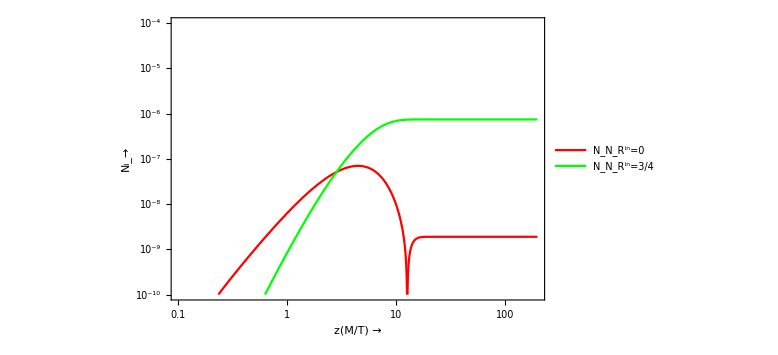

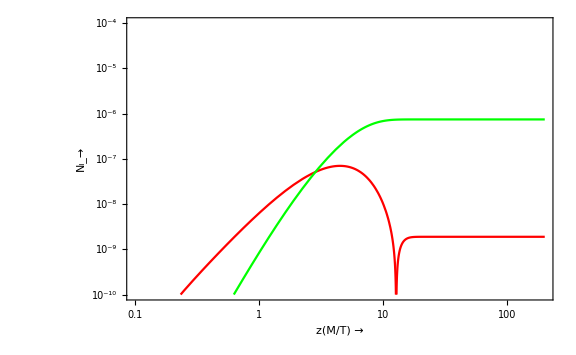

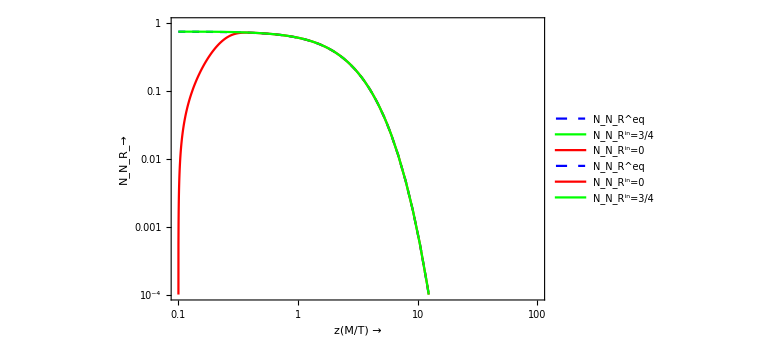

```mathematica
Parameters={Γ->10^-9  , g-> 106.75 , Mpl-> 1.221*10^19, ϵ-> 10^-6};
 M=  3000;
solution= NDSolve[{Nn'[z]== -z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z])*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nl'[z]== -(1/2)*(z * (Γ*0.5*(1-ϵ)/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*((3/8)*z^2*BesselK[2,z]/(3/4))*Nl[z] +ϵ*(z * (Γ/((4 π^3*g/45)^0.5*(M^2/Mpl)))* (BesselK[1,z]/BesselK[2,z]))*(Nn[z]-(3/8)*z^2*BesselK[2,z]), Nn[0.1]==3/4, Nl[0.1]==0}/.Parameters,{Nn[z], Nl[z]},{z, 0.1, 100}];
LogLogPlot[Evaluate[Abs[Nl[z]]/.solution],{z, 0.1,100},PlotRange->{{0.1,100},{10^-10,10^4}}, Frame-> True,PlotStyle->Red,PlotLegends->{"N_l"},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →",""},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];


LogLogPlot[25*z^3*BesselK[1,z],{z,0.01,100},PlotRange->{{0.1,100},{10^-10,10^4}}, Frame-> True,PlotStyle->Green,PlotLegends->{"W_ID"},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →",""},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[1,{z,0.01,100},PlotRange->{{0.1,100},{10^-10,10^4}}, Frame-> True,PlotStyle->{Black, Dashed},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →",""},LabelStyle->Directive[Black,Bold, Medium,15],ImageSize->Large];
LogLogPlot[100*z^2*BesselK[1,z]/BesselK[2,z],{z,0.01,100},PlotRange->{{0.1,100},{10^-10,10^4}}, Frame-> True,GridLines->{{22.9},{}},GridLinesStyle->Directive[Orange, Dashed] ,PlotStyle->Blue,PlotLegends->{"Γ_D/H"},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →",""},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
LogLogPlot[Evaluate[(Nn[z]-(3/8)*z^2*BesselK[2,z])/.solution],{z, 0.1,100},PlotRange->{{0.1,100},{10^-10,10^4}}, Frame-> True,PlotStyle->Yellow,PlotLegends->{"ΔN_N_R"},FrameTicksStyle->Directive[Black,15],FrameLabel->{"z(M/T) →",""},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large];
Show[%,%%,%%%,%%%%,%%%%%]
```